0.442857

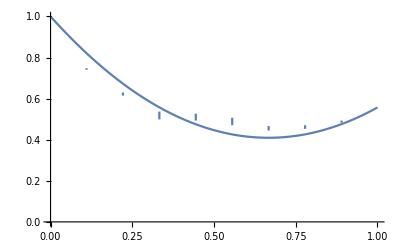

```mathematica
Needs["ErrorBarPlots`"];
location = "/Disk/ds-sopa-personal/s1373240/research/batchJobs/tests/test2/4/";
data = Import[location<>"overallData.dat", "Data"];
settings = Import[location<>"0/0/settings", "Data"];
λ = settings[[3]][[3]];
ζ = 1-λ
p1 = ErrorListPlot[data,PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1}, {0, 1}}];
p2 = Plot[1+ζ ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1}}];
Show[{p1, p2}]
(*trajData = Table[Import[location<>"/"<>ToString[i]<>"/"<>ToString[j]<>"/typeStats.dat", "Data"], {i,0, 16}, {j, 0, 16}];
Manipulate[ListDensityPlot[trajData[[i]][[j]], InterpolationOrder->0, ColorFunction->"GrayTones", PlotRange->{0,1}], {i, 1, 8, 1}, {j, 1, 8, 1}]*)
```

```mathematica
Manipulate[Plot[1+ζ ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{0,2}], {ζ, 0, 1}]
```

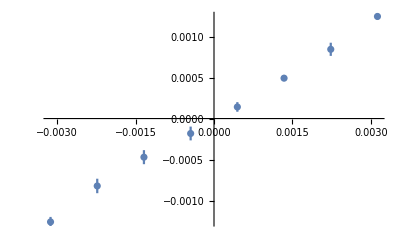

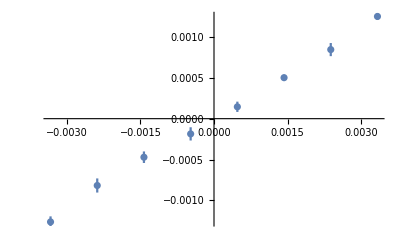

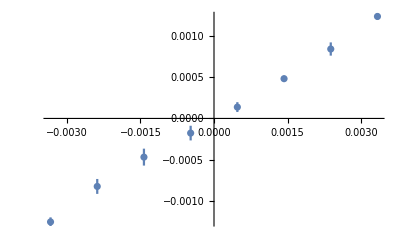

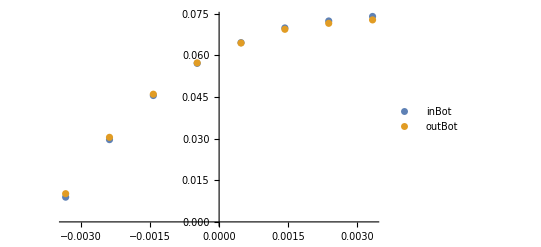

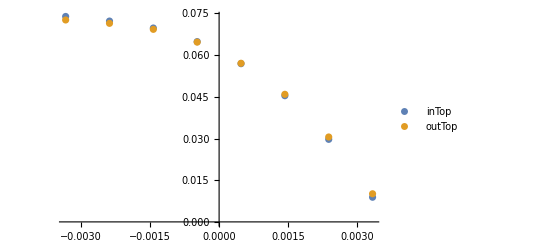

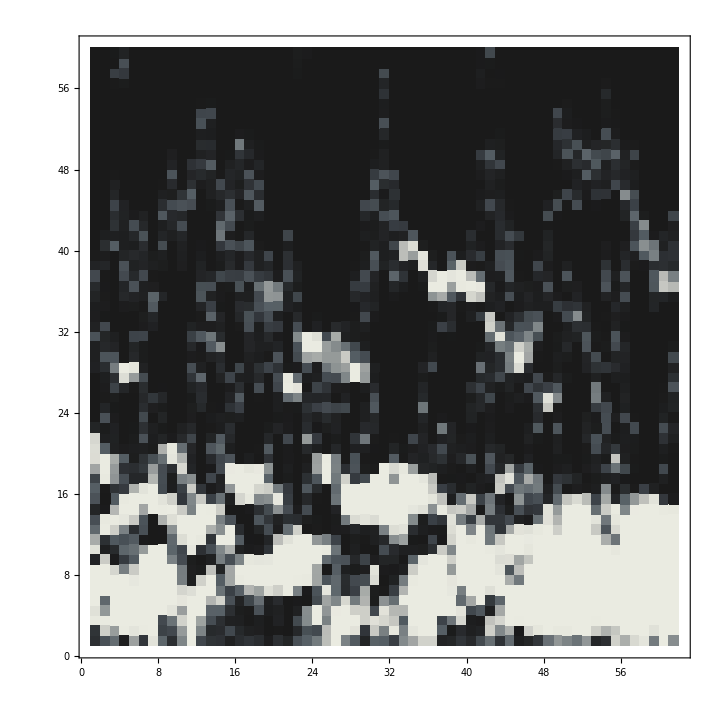

```mathematica
Needs["ErrorBarPlots`"];
location = "/Disk/ds-sopa-personal/s1373240/research/batchJobs/tests/test2/0/0/";
totFlowData = Import[location<>"mathFormatData.dat", "Data"];
ErrorListPlot[totFlowData]
topFlowData = Import[location<>"topFlowData.dat", "Data"];
ErrorListPlot[topFlowData]
botFlowData = Import[location<>"botFlowData.dat", "Data"];
ErrorListPlot[botFlowData]
inBotData = Import[location<>"inBotData.dat", "Data"];
outBotData = Import[location<>"outBotData.dat", "Data"];
ErrorListPlot[{inBotData, outBotData}, PlotLegends->{"inBot", "outBot"}]
inTopData = Import[location<>"inTopData.dat", "Data"];
outTopData = Import[location<>"outTopData.dat", "Data"];
ErrorListPlot[{inTopData, outTopData}, PlotLegends->{"inTop", "outTop"}]
trajData = Import[location<>"0/typeStats.dat", "Data"];
ListDensityPlot[trajData, InterpolationOrder->0, ColorFunction->"GrayTones", PlotRange->{0,1}]
```